```mathematica
SetDirectory[NotebookDirectory[]];
```

### I1

Breaking up the delta function

```mathematica
f[x_,p_]:=p-(4(1-x))/(2-x)^2
roots=Solve[f[x,p]==0,x]
```

{{x→(2 (-1-√(1-p)+p))/p},{x→(2 (-1+√(1-p)+p))/p}}

```mathematica
r1=x/.roots[[2]]
d1=FullSimplify[D[f[x,p],x]/.{x->r1}]
```

(2 (-1+√(1-p)+p))/p

2 (1+√(1-p))-(2+√(1-p)) p

```mathematica
r2=x/.roots[[1]]
d2=FullSimplify[D[f[x,p],x]/.{x->r2}]
```

(2 (-1-√(1-p)+p))/p

2-2 √(1-p)+(-2+√(1-p)) p

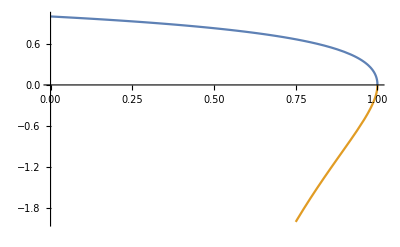

```mathematica
Plot[{r1/.{p->p1},r2/.{p->p1}},{p1,0,1},PlotRange->{-2,1}]
```

Setting up bounds of integration

```mathematica
Reduce[r1>(2-r1)/2,p]
```

p<0||0<p<3/4

```mathematica
Reduce[{(2-r1)(1-z)<r1},p]
```

(z≤0&&p<2 z-z^2)||(0<z≤1&&(p<0||0<p<2 z-z^2))||(z>1&&(p<0||0<p≤1))

```mathematica
Reduce[1-r1<(2-r1)/2,p]
```

p<0||0<p<1

```mathematica
Reduce[r1<1,p]
```

0<p≤1

```mathematica
Reduce[(2-r1)/2>0,p]
```

p<0||0<p≤1

```mathematica
Reduce[(2-r1)(1-z)<1,p]
```

(z≤0&&p<4 z-4 z^2)||(0<z≤1/2&&(p<0||0<p<4 z-4 z^2))||(z>1/2&&(p<0||0<p≤1))

```mathematica
Reduce[4z-4z^2>2z-z^2,z]
```

0<z<2/3

Solving the integral (by hand)

Part one

```mathematica
FullSimplify[1/(r1-1)]
```

p/(-2+2 √(1-p)+p)

```mathematica
FullSimplify[r1-2]
```

(2 (-1+√(1-p)))/p

```mathematica
FullSimplify[(r1-1)^2/2-r1^2/8]
```

(6-6 √(1-p)-5 p+2 √(1-p) p)/(2 p^2)

```mathematica
FullSimplify[Expand[FullSimplify[1+r1^2]]]
```

(8-8 √(1-p)+p (-12+8 √(1-p)+5 p))/p^2

```mathematica
FullSimplify[(r1-1)/(-(r1/2))]
```

-1+1/(√(1-p))

```mathematica
Reduce[{0<p<1,p(2+√(1-p))>2(1-√(1-p))},p]
```

0<p<1

```mathematica
FullSimplify[d1*(p-2+2 √(1-p))]
```

-√(1-p) p^2

Solving with Mathematica

```mathematica
i1part1=FullSimplify[1/d1 Assuming[0<r<2/3,FullSimplify[Integrate[(r^2+x^2)/((1-r)(1-x)),{x,(2-r)/2,r}]]]/.{r->r1}]
```

1/(2 √(1-p) p^3)(6 (-1+√(1-p))+(17-14 √(1-p)-8 p) p-2 (8-8 √(1-p)+p (-12+8 √(1-p)+5 p)) Log[-2+p/(-1+√(1-p)+p)])

```mathematica
i1part2=FullSimplify[1/d1 Assuming[{0<z<1/2,r>(-1+2 z)/(-1+z),0<r<1},FullSimplify[Integrate[(r^2+x^2)/((1-r)(1-x)),{x,(2-r)/2,(2-r)(1-z)}]]]/.{r->r1}]
```

1/(2 √(1-p) p^3)(-6+6 √(1-p)+2 √(1-p) p+p (1-2 z)^2+16 z-16 √(1-p) z-4 √(1-p) p z-8 z^2+8 √(1-p) z^2-p^2 Log[4]+2 p^2 Log[(2 (-1+√(1-p)+p))/p]-2 p^2 Log[1-(2 (-1+√(1-p)) (-1+z))/p]-8 (-1+p) (-2+2 √(1-p)+p) Log[(-1+√(1-p)+p-2 √(1-p) z)/(-1+p)])

```mathematica
i1=FullSimplify[HeavisideTheta[3/4-p]HeavisideTheta[p-(2z-z^2)]i1part1+HeavisideTheta[(2z-z^2)-p]i1part2]
```

1/(2 √(1-p) p^3)(-6 HeavisideTheta[3/4-p,p+(-2+z) z]+HeavisideTheta[3/4-p,p+(-2+z) z] (6 √(1-p)+(17-14 √(1-p)-8 p) p-2 (8-8 √(1-p)+p (-12+8 √(1-p)+5 p)) Log[-2+p/(-1+√(1-p)+p)])+HeavisideTheta[-p-(-2+z) z] (-(-1+2 z) (p (1+2 √(1-p)-2 z)-2 (-1+√(1-p)) (-3+2 z))+2 p^2 Log[(-1+√(1-p)+p)/p]-2 p^2 Log[1-(2 (-1+√(1-p)) (-1+z))/p]-8 (-1+p) (-2+2 √(1-p)+p) Log[(-1+√(1-p)+p-2 √(1-p) z)/(-1+p)]))

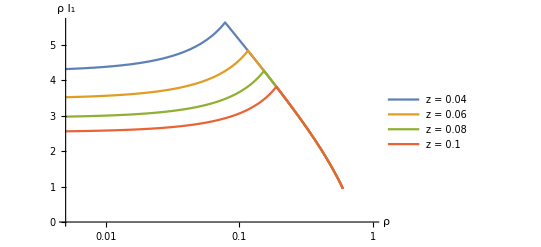

```mathematica
firstPlot=LogLinearPlot[{p1*i1/.{p->p1,z->0.04},p1*i1/.{p->p1,z->0.06},p1*i1/.{p->p1,z->0.08},p1*i1/.{p->p1,z->0.1}},{p1,0.005,0.6},PlotRange->{0,Automatic},AxesLabel->{"ρ","ρ I_1"},PlotLegends->{"z = 0.04", "z = 0.06", "z = 0.08", "z = 0.1"}]
```

```mathematica
(*Export["i1_first_look.pdf",firstPlot]*)
```

### I2

Setup bounds of integration

```mathematica
Reduce[2(1-r1)>(2-r1)z,p]
```

(z≤0&&(2 z-z^2<p<0||0<p≤1))||(0<z<1&&2 z-z^2<p≤1)

```mathematica
Reduce[(2-r1)/2>2(1-r1),p]
```

p<0||0<p<3/4

```mathematica
Reduce[(2-r1)/2>(2-r1)z,p]
```

z<1/2&&(p<0||0<p≤1)

Integrate

```mathematica
i2part1=FullSimplify[Assuming[0<p<3/4,1/Abs[d1] Integrate[(r1^2+x^2)/((1-r1)(1-x)),{x,2(1-r1),(2-r1)/2}]]]
```

(5-10 √(1-p)+2 (6+2 √(1-p)-5 p) Log[3-1/(√(1-p))])/(2 p Abs[2 (1+√(1-p))-(2+√(1-p)) p])

```mathematica
i2part2=FullSimplify[Assuming[{0<p<1,0<z<1/2,p<2z-z^2},1/Abs[d1] Integrate[(r1^2+x^2)/((1-r1)(1-x)),{x,(2-r1)z,(2-r1)/2}]]]
```

((-1+2 z) (3+2 √(1-p)+2 z)+2 (6+2 √(1-p)-5 p) Log[p]-2 (6+2 √(1-p)-5 p) Log[-1+√(1-p)+p]+2 (6+2 √(1-p)-5 p) Log[1+(2 (-1+√(1-p)) z)/p])/(2 p Abs[2 (1+√(1-p))-(2+√(1-p)) p])

### I5

```mathematica
g[x2_]:=p-(4(x1+x2-1))/(x1+x2)^2
```

```mathematica
roots5=Solve[g[x2]==0,x2];
s1=x2/.roots5[[2]]
s2=x2/.roots5[[1]]
```

(2+2 √(1-p)-p x1)/p

(2-2 √(1-p)-p x1)/p

```mathematica
sigma1=FullSimplify[g'[s1]]
sigma2=FullSimplify[g'[s2]]
```

-2+2 √(1-p)+2 p-√(1-p) p

-2 (1+√(1-p))+(2+√(1-p)) p

```mathematica
Reduce[{0<s1<1,0<x1<1,0<p<1},p]
Reduce[{0<s2<1,0<x1<1,0<p<1},p]
```

False

0<x1<1&&0<p<(4 x1)/(1+2 x1+x1^2)

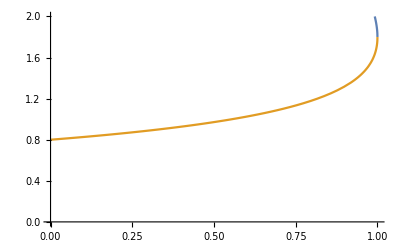

```mathematica
Plot[{s1/.{p->p1,x1->0.2},s2/.{p->p1,x1->0.2}},{p1,0,1},PlotRange->{0,2}]
```

Simplifying Heaviside functions

```mathematica
Reduce[(2-2 √(1-p))/p>1,p]
```

0<p≤1

```mathematica
FullSimplify[Reduce[{0<z<1,0<p<1,s2/(x1+s2)>z},x1]]
```

0<z<1&&0<p<1&&x1<(2 (-1+√(1-p)) (-1+z))/p

```mathematica
b1=(2 (-1+√(1-p)) (-1+z))/p;
```

```mathematica
FullSimplify[Reduce[{0<p<1,2-s2>2x1},x1]]
```

0<p<1&&x1<(2 (-1+√(1-p)+p))/p

```mathematica
b2=(2 (-1+√(1-p)+p))/p;
```

```mathematica
FullSimplify[Reduce[{0<p<1,x1>s2},x1]]
```

0<p<1&&√((1-p)/p^2)+x1>1/p

```mathematica
b3=(1-√(1-p))/p;
```

Figuring out integration bounds

```mathematica
Reduce[{0<z<1,(2 (-1+√(1-p)) (-1+z))/p<(2 (-1+√(1-p)+p))/p},p]
```

0<z<1&&(p<0||0<p<2 z-z^2)

```mathematica
Reduce[{(2 (-1+√(1-p)+p))/p>(1-√(1-p))/p,0<p<1},p]
```

0<p<3/4

Perform integration

```mathematica
i5part1=FullSimplify[Assuming[0<p<3/4,1/Abs[sigma2] Integrate[(s2^2+x1^2)/((1-s2)(1-x1)),{x1,b3,b2}]]]
```

(2 (-1+√(1-p)) (-2+p) ArcTanh[1/2 (1+√(1-p))]-2 (-6 √(1-p)-6 p+4 √(1-p) p+Log[1-p]+2 Log[2-2 √(1-p)-p]+Log[2-2 √(1-p)+p]-2 (-3+Log[-1+√(1-p)+p]+Log[-4+4 √(1-p)+3 p]))-(-2 √(1-p)+(-1+√(1-p)) p) (Log[1-p]+2 Log[2-2 √(1-p)-p]+Log[2-2 √(1-p)+p]-2 (Log[-1+√(1-p)+p]+Log[-4+4 √(1-p)+3 p])))/(2 √(1-p) p Abs[-2 (1+√(1-p))+(2+√(1-p)) p])

```mathematica
i5part2=FullSimplify[Assuming[{0<p<1,0<z<1/2,p<2z-z^2},1/Abs[sigma2] Integrate[(s2^2+x1^2)/((1-s2)(1-x1)),{x1,b3,b1}]]]
```

(2 (-1+√(1-p)) (-2+p) ArcTanh[1/2 (1+√(1-p))]-2 (-1+√(1-p)) (-2+p) ArcTanh[1-(p-2 z)/(2 √(1-p))-z]-(-2 √(1-p)+(-1+√(1-p)) p) (Log[-((-1+p) (2-2 √(1-p)+p))/p]-2 Log[(-1+√(1-p)+p)/p]+2 Log[1-(2 (-1+√(1-p)) (-1+z))/p]-Log[-p-4 (√(1-p)-z) (-1+z)+(8 (-1+√(1-p)) (-1+z) z)/p])+2 (2 (-1+√(1-p)+p) (-1+2 z)-Log[-((-1+p) (2-2 √(1-p)+p))/p]+2 Log[(-1+√(1-p)+p)/p]-2 Log[1-(2 (-1+√(1-p)) (-1+z))/p]+Log[-p-4 (√(1-p)-z) (-1+z)+(8 (-1+√(1-p)) (-1+z) z)/p]))/(2 √(1-p) p Abs[-2 (1+√(1-p))+(2+√(1-p)) p])

### Putting it together

```mathematica
part1=Assuming[0<p<3/4,FullSimplify[2i1part1+2i2part1+2i5part1]]
```

(√(1-p) p^2 (5-10 √(1-p)+2 (6+2 √(1-p)-5 p) Log[3-1/(√(1-p))])+p^2 (2 (-1+√(1-p)) (-2+p) ArcTanh[1/2 (1+√(1-p))]-(-2 √(1-p)+(-1+√(1-p)) p) (Log[1-p]+2 Log[2-2 √(1-p)-p]+Log[2-2 √(1-p)+p]-2 Log[(-1+√(1-p)+p) (-4+4 √(1-p)+3 p)])-2 (6-6 √(1-p)-6 p+4 √(1-p) p+2 Log[2-2 √(1-p)-p]+Log[-(-1+p) (2-2 √(1-p)+p)]-2 Log[(-1+√(1-p)+p) (-4+4 √(1-p)+3 p)]))+(2 (1+√(1-p))-(2+√(1-p)) p) (6 (-1+√(1-p))+(17-14 √(1-p)-8 p) p-2 (8-8 √(1-p)+p (-12+8 √(1-p)+5 p)) Log[-2+p/(-1+√(1-p)+p)]))/(√(1-p) p^3 (2 (1+√(1-p))-(2+√(1-p)) p))

```mathematica
part2=2i1part2+2i2part2+2i5part2;
```

```mathematica
total=HeavisideTheta[3/4-p]HeavisideTheta[p-(2z-z^2)]part1+HeavisideTheta[(2z-z^2)-p]part2;
```

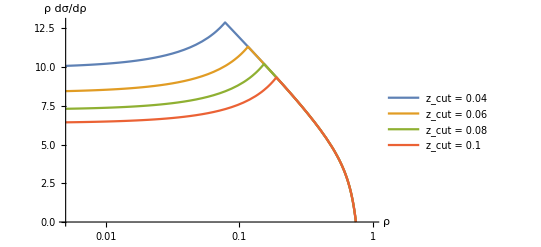

```mathematica
totalPlot=LogLinearPlot[{p1 total/.{p->p1,z->0.04},p1 total/.{p->p1,z->0.06}, p1 total/.{p->p1,z->0.08},p1 total/.{p->p1,z->0.1}},{p1,0.005,0.75},PlotRange->{0,Automatic},
AxesLabel->{"ρ","ρ dσ/dρ"},PlotLegends->{"z_cut = 0.04", "z_cut = 0.06", "z_cut = 0.08", "z_cut = 0.1"}]
```

```mathematica
Export["plots/first_reproduction.pdf",totalPlot]
Export["plots/first_reproduction.png",totalPlot]
```

plots/first_reproduction.pdf

plots/first_reproduction.png

## Limits

Where x1 and x3 have different lambdas

```mathematica
FullSimplify[Expand[x1^2+(x1+x3-2)^2/.{x1->1-λ1(1-x1),x3->λ3 x3}]]
```

2+2 (-1+x1)^2 λ1^2+2 (-1+x1) x3 λ1 λ3+x3 λ3 (-2+x3 λ3)

```mathematica
Expand[(1-x1)(x1+x3-1)/.{x1->1-λ1(1-x1),x3->λ3 x3}]
```

-λ1^2+2 x1 λ1^2-x1^2 λ1^2+x3 λ1 λ3-x1 x3 λ1 λ3

Where x1 and x3 have the same lambdas

```mathematica
Expand[x1^2+(x1+x3-2)^2/.{x1->1-λ(1-x1),x3->λ x3}]/.λ^b_/;b≥2->0
```

2-2 x3 λ

```mathematica
FullSimplify[Expand[(1-x1)(x1+x3-1)/.{x1->1-λ(1-x1),x3->λ x3}]]
```

-(-1+x1) (-1+x1+x3) λ^2

Plotting

```mathematica
Manipulate[
LogLogPlot[{(x1^2+(x1+x3-2)^2)/((1-x1)(x1+x3-1))/.{x1->x1val},(2+2x3(x1-2))/(x3(1-x1))/.{x1->x1val},(2-2x3)/((1-x1)(x1+x3-1))/.{x1->x1val}},{x3,0.01,0.8},PlotLegends->{"True", "Different lambdas", "Same lambdas"},PlotLabel->"x1 = " <> ToString[x1val],AxesLabel->{"x3", "integrand"} ],{x1val,0.8,0.99999}]
```

It seems that we should take x1 and x3 to scale with the same lambda

Now we want to figure out how to approximate ρ

```mathematica
Series[r1/.{p->λp p},{λp,0,3}]
```

1-(p λp)/4-(p^2 λp^2)/8-(5 p^3 λp^3)/64+O[λp]^4

```mathematica
Expand[4(1-x1)/.{x1->1-λ(1-x1)}]
Expand[(2-x1)^2/.{x1->1-λ(1-x1)}]/.λ^b_/;b≥2->0
```

4 λ-4 x1 λ

1+2 λ-2 x1 λ

Getting it another way:

```mathematica
Series[(3p-4)/(2p-4),{p,0,4}]
```

1-p/4-p^2/8-p^3/16-p^4/32+O[p]^5

Thus we conclude that the delta function asserts x1 = 1 - ρ/4

```mathematica
Series[d1/.{p->λp p},{λp,0,3}]
```

4-4 p λp+(p^2 λp^2)/4+O[λp]^4

Now we simplify things after asserting the delta function

```mathematica
Expand[(λ^2(1-x1)(x1+x3-1))(4-4p λp)/.{x1->1-p/4 λp}]/.λp^b_/;b≥2->0
```

p x3 λ^2 λp

```mathematica
FullSimplify[(λ x3)/(2-x1)/.{x1->1-p/4 λp}]
```

(4 x3 λ)/(4+p λp)

```mathematica
FullSimplify[2r+x3-2/.{r->1-p λ/4,x3->λ x3}]
```

-(p λ)/2+x3 λ

```mathematica
Assuming[0<p<1,Integrate[(2(1-x3))/(p x3),{x3,p/2,(4+p)/8}]]
```

(-4+3 p+8 Log[1/4+1/p])/(4 p)

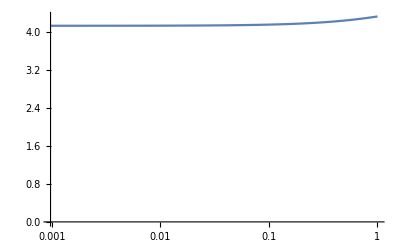

```mathematica
LogLinearPlot[-p(4+p-8 z-8 Log[(4+p)/(8 z)])/(4 p)/.z->0.04,{p,0,1},PlotRange->{0,Automatic}]
```

### Limits, round 2

```mathematica
Expand[x1^2+(2-x1-x3)^2/.{x1->1-λ(1-x1),x3->λ x3}]/.λ^b_/;b≥2->0
```

2-2 x3 λ

```mathematica
FullSimplify[Expand[(1-x1)(x1+x3-1)/.{x1->1-λ(1-x1),x3->λ x3}]]
```

-(-1+x1) (-1+x1+x3) λ^2

```mathematica
Series[(x1^2+(2-x1-x3)^2)/((1-x1)(x1+x3-1))/.{x1->1-λ(1-x1),x3->λ x3},{λ,0,3}]
```

-2/(((-1+x1) (-1+x1+x3)) λ^2)+(2 x3)/((-1+x1) (-1+x1+x3) λ)+((-1+x1)^2+(1-x1-x3)^2)/((1-x1) (-1+x1+x3))+O[λ]^4